```mathematica
M = {{-α,κ},{α,-2*κ}};
```

```mathematica
c = Simplify[Integrate[MatrixExp[-M*t].{{2*Subscript[T, 1],-2*Subscript[T, 1]},{-2*Subscript[T, 1],2*(Subscript[T, 1]+Subscript[T, 2])}}.Transpose[MatrixExp[-M*t]],{t,-∞,0},Assumptions->{α>0,κ>0,Subscript[T, 1]>0,Subscript[T, 2]>0}],{α>0,κ>0,Subscript[T, 1]>0,Subscript[T, 2]>0}]
```

{{((α+κ) T_1+κ T_2)/(α (α+2 κ)),(-T_1+T_2)/(α+2 κ)},{(-T_1+T_2)/(α+2 κ),(κ T_1+(α+κ) T_2)/(κ (α+2 κ))}}

```mathematica
p = Exp[-{x,s}.Inverse[c].{x,s}/2]
```

ⅇ^(1/2 (-s (-(x (-T_1+T_2))/((α+2 κ) ((κ T_1^2)/(α (α+2 κ)^2)+(4 T_1 T_2)/(α+2 κ)^2+(α T_1 T_2)/(κ (α+2 κ)^2)+(2 κ T_1 T_2)/(α (α+2 κ)^2)+(κ T_2^2)/(α (α+2 κ)^2)))+(s ((α+κ) T_1+κ T_2))/(α (α+2 κ) ((κ T_1^2)/(α (α+2 κ)^2)+(4 T_1 T_2)/(α+2 κ)^2+(α T_1 T_2)/(κ (α+2 κ)^2)+(2 κ T_1 T_2)/(α (α+2 κ)^2)+(κ T_2^2)/(α (α+2 κ)^2))))-x (-(s (-T_1+T_2))/((α+2 κ) ((κ T_1^2)/(α (α+2 κ)^2)+(4 T_1 T_2)/(α+2 κ)^2+(α T_1 T_2)/(κ (α+2 κ)^2)+(2 κ T_1 T_2)/(α (α+2 κ)^2)+(κ T_2^2)/(α (α+2 κ)^2)))+(x (κ T_1+(α+κ) T_2))/(κ (α+2 κ) ((κ T_1^2)/(α (α+2 κ)^2)+(4 T_1 T_2)/(α+2 κ)^2+(α T_1 T_2)/(κ (α+2 κ)^2)+(2 κ T_1 T_2)/(α (α+2 κ)^2)+(κ T_2^2)/(α (α+2 κ)^2))))))

```mathematica
jx = FullSimplify[(κ*s-α*x)*p-Subscript[T, 1]*D[p,x]+Subscript[T, 1] D[p,s],{α>0,κ>0,Subscript[T, 1]>0,Subscript[T, 2]>0}]
```

-(ⅇ^(-((α+2 κ) (κ ((s+x)^2 α+s^2 κ) T_1+(-2 s x α κ+s^2 κ^2+x^2 α (α+κ)) T_2))/(2 (κ^2 T_1^2+(α^2+4 α κ+2 κ^2) T_1 T_2+κ^2 T_2^2))) κ^2 (T_1-T_2) ((x α+s (α+κ)) T_1+(-x α+s κ) T_2))/(κ^2 T_1^2+(α^2+4 α κ+2 κ^2) T_1 T_2+κ^2 T_2^2)

```mathematica
js  = FullSimplify[(-2*κ*s+α*x)*p-(Subscript[T, 1]+Subscript[T, 2])*D[p,s]+Subscript[T, 1] D[p,x],{α>0,κ>0,Subscript[T, 1]>0,Subscript[T, 2]>0}]
```

(ⅇ^(-((α+2 κ) (κ ((s+x)^2 α+s^2 κ) T_1+(-2 s x α κ+s^2 κ^2+x^2 α (α+κ)) T_2))/(2 (κ^2 T_1^2+(α^2+4 α κ+2 κ^2) T_1 T_2+κ^2 T_2^2))) α κ (T_1-T_2) ((s+x) κ T_1+(-s κ+x (α+κ)) T_2))/(κ^2 T_1^2+(α^2+4 α κ+2 κ^2) T_1 T_2+κ^2 T_2^2)

```mathematica
ω =Simplify[Curl[{jx,js},{x,s}],{α>0,κ>0,Subscript[T, 1]>0,Subscript[T, 2]>0}]
```

-1/((κ^2 T_1^2+(α^2+4 α κ+2 κ^2) T_1 T_2+κ^2 T_2^2)^2)ⅇ^(-((α+2 κ) (κ ((s+x)^2 α+s^2 κ) T_1+(-2 s x α κ+s^2 κ^2+x^2 α (α+κ)) T_2))/(2 (κ^2 T_1^2+(α^2+4 α κ+2 κ^2) T_1 T_2+κ^2 T_2^2))) κ (T_1-T_2) (-κ^3 (2 α+κ) T_1^3+T_2^2 ((α+2 κ) (s^2 κ^2 (α^2+κ^2)-2 s x α κ (α^2+α κ+κ^2)+x^2 α^2 (α^2+2 α κ+2 κ^2))-κ^2 (α^2+α κ+κ^2) T_2)+κ T_1^2 (κ (α+2 κ) (2 x^2 α^2+2 s x α (2 α+κ)+s^2 (2 α^2+2 α κ+κ^2))-(2 α^3+10 α^2 κ+9 α κ^2+3 κ^3) T_2)-T_1 T_2 (-2 κ (α+2 κ) (x^2 α^3+s x α^2 (α-κ)+s^2 κ (-α^2+α κ+κ^2))+(α^4+5 α^3 κ+7 α^2 κ^2+8 α κ^3+3 κ^4) T_2))

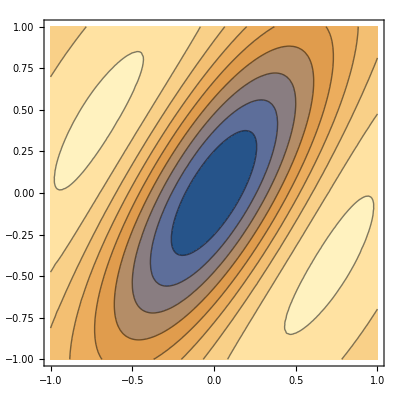

```mathematica
ContourPlot[ω/.{Subscript[T, 1]->0.1,Subscript[T, 2]->1,α->1,κ->1},{x,-1,1},{s,-1,1},PlotRange->All]
```

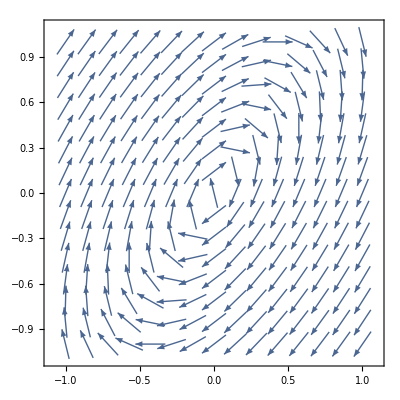

```mathematica
VectorPlot[1*Normalize[{jx/.{Subscript[T, 1]->0.1,Subscript[T, 2]->1,α->1,κ->1},js/.{Subscript[T, 1]->0.1,Subscript[T, 2]->1,α->1,κ->1}}],{x,-1,1},{s,-1,1}]
```

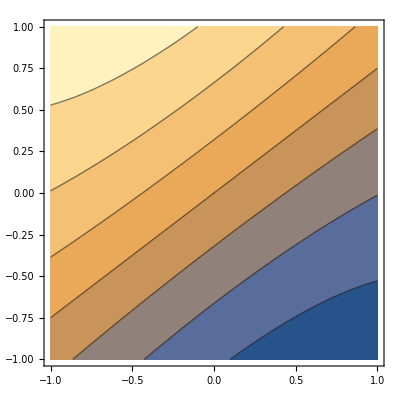

```mathematica
ContourPlot[jx/.{Subscript[T, 1]->0.1,Subscript[T, 2]->1,α->.1,κ->.1},{x,-1,1},{s,-1,1},PlotRange->All]
```

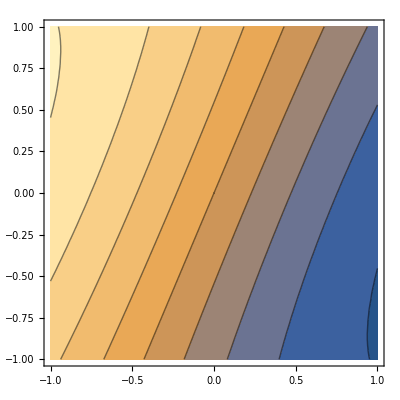

```mathematica
ContourPlot[js/.{Subscript[T, 1]->.1,Subscript[T, 2]->1,α->.1,κ->.1},{x,-1,1},{s,-1,1},PlotRange->All]
```

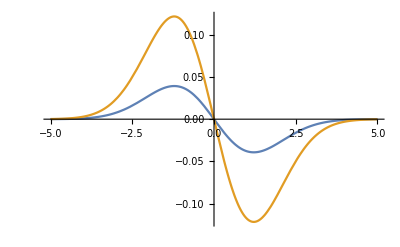

```mathematica
Plot[{jx/.{Subscript[T, 1]->0.5,Subscript[T, 2]->1,α->0.5,κ->10,s->0},js/.{Subscript[T, 1]->0.5,Subscript[T, 2]->1,α->0.5,κ->10,s->0}},{x,-5,5},PlotRange->All]
```